# Hoja 3: Derivación e integración.

## Ejercicio 1

Para y=x^3 representamos la función en Mathematica.

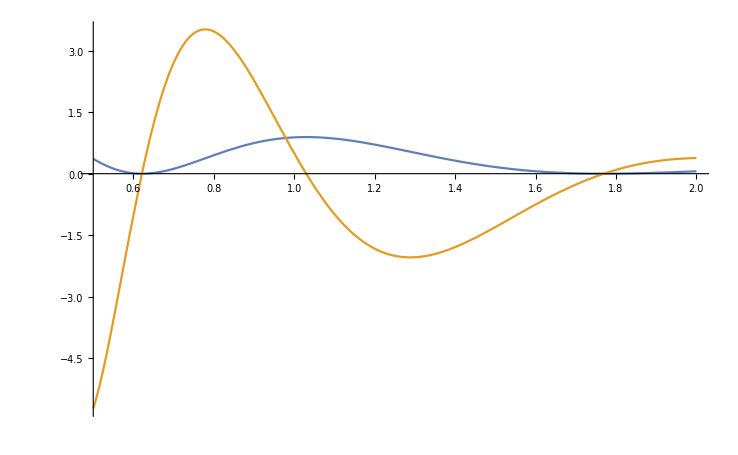

0.492431480686

```mathematica
y[x_]:=x^3
f[x_]:=Exp[-y[x]/10]*Cos[Log[y[x]]+3]^2;

Plot[{f[x],f'[x]},{x,0.5,2}]
N[f'[1],12]
```

A continuación hallamos su derivada en el punto x=1. Después utilizaremos este valor para poder calcular el error relativo en Fortran.

0.492431480686

Realizamos los mismo cálculos para y=1+x^2. No aparece explícitamente calculado en el 3.1 de Fortran sería simplemente cambiar el valor de y(x) y volver a ejecutar el programa :

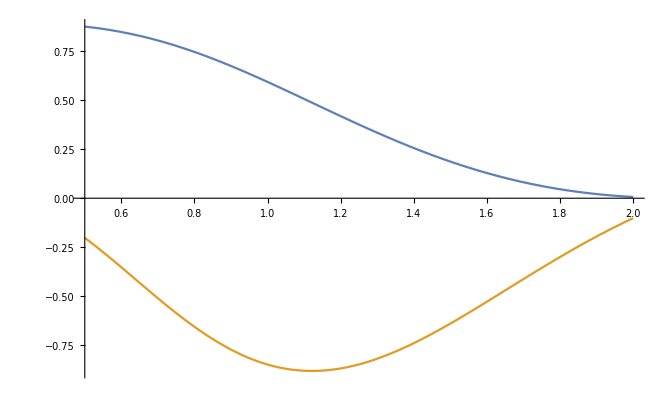

-0.84959331437

```mathematica
h[x_]:=x^2+1
m[x_]:=Exp[-h[x]/10]*Cos[Log[h[x]]+3]^2;

Plot[{m[x],m'[x]},{x,0.5,2}]
N[m'[1],12]
```

A continuación vamos a adjuntar la tabla con los resultados obtenidos en Fortran mediante los  tres métodos con sus correspondientes errores relativos:

```mathematica
SetDirectory[NotebookDirectory[]];
deriv1=Import ["derivadas1.txt","Table"];
TableForm[deriv1,TableHeadings->{{"0.01","0.009","0.008","0.007","0.006","0.005","0.004","0.003","0.002","0.001"},{"No sim","Sim","Richard","Error no sim","Error sim","Error Richard"}}]
```

| No sim | Sim | Richard | Error no sim | Error sim | Error Richard
0.01 | 0.406511 | 0.493008 | 0.492432 | 17.4481 | 0.117166 | 0.0000241731
0.009 | 0.415047 | 0.492899 | 0.492432 | 15.7147 | 0.0949196 | 0.0000158602
0.008 | 0.423596 | 0.492801 | 0.492432 | 13.9786 | 0.0750088 | 9.9016×10^-6
0.007 | 0.432158 | 0.492714 | 0.492432 | 12.24 | 0.0574357 | 5.8042×10^-6
0.006 | 0.440732 | 0.492639 | 0.492431 | 10.4988 | 0.0422022 | 3.133×10^-6
0.005 | 0.449318 | 0.492576 | 0.492431 | 8.75516 | 0.0293097 | 1.5109×10^-6
0.004 | 0.457917 | 0.492524 | 0.492431 | 7.00899 | 0.0187596 | 6.189×10^-7
0.003 | 0.466528 | 0.492483 | 0.492431 | 5.26036 | 0.0105529 | 1.958×10^-7
0.002 | 0.475151 | 0.492455 | 0.492431 | 3.5093 | 0.00469037 | 3.87×10^-8
0.001 | 0.483785 | 0.492437 | 0.492431 | 1.75584 | 0.00117262 | 2.4×10^-9

```mathematica
SetDirectory[NotebookDirectory[]];
deriv2=Import ["derivadas2.txt","Table"];
TableForm[deriv2,TableHeadings->{{"0.01","0.009","0.008","0.007","0.006","0.005","0.004","0.003","0.002","0.001"},{"No sim","Sim","Richard","Error no sim","Error sim","Error Richard"}}]
```

| No sim | Sim | Richard | Error no sim | Error sim | Error Richard
0.01 | -0.852223 | -0.849518 | -0.849593 | 0.309472 | 0.0088552 | 1.431×10^-7
0.009 | -0.851966 | -0.849532 | -0.849593 | 0.279323 | 0.0071728 | 9.39×10^-8
0.008 | -0.851709 | -0.849545 | -0.849593 | 0.248996 | 0.00566746 | 5.86×10^-8
0.007 | -0.85145 | -0.849556 | -0.849593 | 0.218492 | 0.00433919 | 3.44×10^-8
0.006 | -0.851189 | -0.849566 | -0.849593 | 0.187811 | 0.003188 | 1.86×10^-8
0.005 | -0.850927 | -0.849575 | -0.849593 | 0.156952 | 0.00221391 | 9.×10^-9
0.004 | -0.850663 | -0.849581 | -0.849593 | 0.125916 | 0.00141691 | 3.7×10^-9
0.003 | -0.850398 | -0.849587 | -0.849593 | 0.0947029 | 0.000797015 | 1.2×10^-9
0.002 | -0.850131 | -0.84959 | -0.849593 | 0.0633124 | 0.00035423 | 3.×10^-10
0.001 | -0.849863 | -0.849593 | -0.849593 | 0.0317448 | 0.0000885576 | 1.×10^-10

## Ejercicio 2

Primero calculamos el valor exacto de la integral, con el que podremos calcular el error relativo:

```mathematica
Integrate[f[x],{x,0.5,2}]
```

0.502441

Para Newton-Cotes calculamos los pesos. Para ello necesitamos resolver un sistema de  6 ecuaciones donde para cada una de ellas evaluamos la función en 5 puntos distintos:

```mathematica
ClearAll;
f0[x_]:=1;
f1[x_]:=x;
f2[x_]:=x^2;
f3[x_]:=x^3;
f4[x_]:=x^4;
f5[x_]:=x^5;
a=0.5;
b=2;
h=(b-a)/5;
x0=a;
x1=a+h;
x2=a+2h;
x3=a+3h;
x4=a+4h;
x5=b;
d0=Integrate[f0[x],{x,a,b}];
d1=Integrate[f1[x],{x,a,b}];
d2=Integrate[f2[x],{x,a,b}];
d3=Integrate[f3[x],{x,a,b}];
d4=Integrate[f4[x],{x,a,b}];
d5=Integrate[f5[x],{x,a,b}];
eq={d0==a0*f0[x0]+a1*f0[x1]+a2*f0[x2]+a3*f0[x3]+a4*f0[x4]+a5*f0[x5],
d1==a0*f1[x0]+a1*f1[x1]+a2*f1[x2]+a3*f1[x3]+a4*f1[x4]+a5*f1[x5],
d2==a0*f2[x0]+a1*f2[x1]+a2*f2[x2]+a3*f2[x3]+a4*f2[x4]+a5*f2[x5],
d3==a0*f3[x0]+a1*f3[x1]+a2*f3[x2]+a3*f3[x3]+a4*f3[x4]+a5*f3[x5],
d4==a0*f4[x0]+a1*f4[x1]+a2*f4[x2]+a3*f4[x3]+a4*f4[x4]+a5*f4[x5],
d5==a0*f5[x0]+a1*f5[x1]+a2*f5[x2]+a3*f5[x3]+a4*f5[x4]+a5*f5[x5]};
Simplify[Solve[eq,{a0,a1,a2,a3,a4,a5}]]
```

```mathematica
{{a0->0.0989583333333346,a1->0.39062499999998795,a2->0.2604166666666992,a3->0.26041666666662844,a4->0.390625000000021,a5->0.09895833333332894}}
```

A continuación se muestra las tablas con los valores obtenidos para las integrales numéricas en cada método para cada y(x):

```mathematica
SetDirectory[NotebookDirectory[]];
tabla=Import ["integrales.txt","Table"];
TableForm[tabla,TableHeadings->{{"Simpson","Newton-Cotes","GaussLegendre","Trapecio NA","Trpaceio A","Simpson NA"},{"Cálculo","Error relativo"}}]
```

| Cálculo | Error relativo
Simpson | 0.718854 | 43.0724
Newton-Cotes | 0.527023 | 4.89247
GaussLegendre | 0.502441 | 9.2×10^-8
Trapecio NA | 0.50364 | 0.238647
Trpaceio A | 0.502431 | 0.00191212
Simpson NA | 0.502438 | 0.000596275

El valor exacto para y(x)=x^3 es 0.5024408625161916 que podemos comparar con los obtenidos en Fortran.

## Ejercicio 3

Hallamos el valor analítico de la integral de superficie:

```mathematica
g[x_,y_]:=(x^2+y^2)*Exp[-x*y]*Sin[y]*Cos[x];
l1[x_]:=0;
l2[x_]:=1+x^2;

i2=NIntegrate[g[x,y],{x,0,2},{y,l1[x],l2[x]},AccuracyGoal->10]
```

0.47478

```mathematica
NumberForm[i2,16]
```

0.4747798814549549

```mathematica
N[i2,10]
```

0.47478

Representamos la función gráficamente con la ayuda de Mathematica:

```mathematica
Plot3D[(x^2+y^2)*Exp[-x*y]*Sin[y]*Cos[x],{x,0,2},{y,0,5}]
```

-Graphics3D-

El resultado obtenido en Fortran y su correspondiente error son:

```mathematica
SetDirectory[NotebookDirectory[]];
intdoble=Import ["integraldoble.txt"]
```

0.4747798116   0.0000396861